# Platonic Solid

### Author

Eric W. Weisstein
August 31, 2026

This notebook downloaded from https://mathworld.wolfram.com/notebooks/Polyhedra/PlatonicSolid.nb.

For more information, see Eric's MathWorld entry https://mathworld.wolfram.com/PlatonicSolid.html.

©2026 Wolfram Research, Inc. except for portions noted otherwise

## Figure

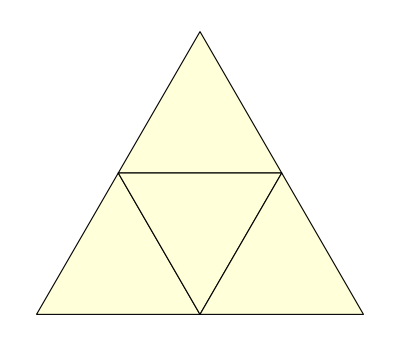
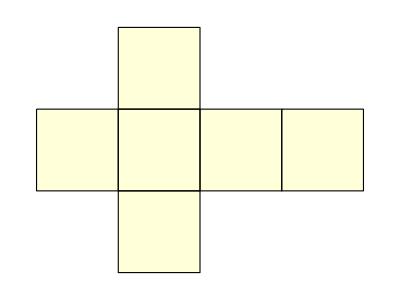
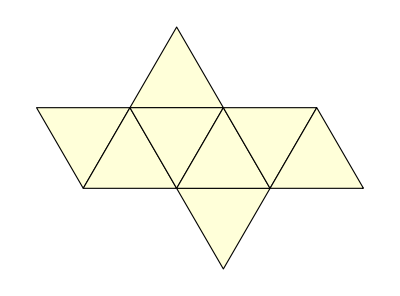
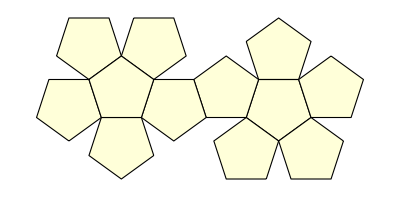
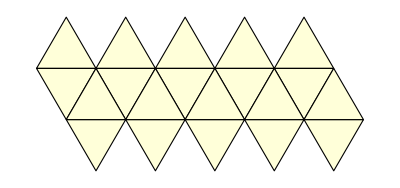
regular tetrahedron | cube | regular octahedron | regular dodecahedron | regular icosahedron
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{
Thread[Style[PolyhedronData["Platonic","Name"],Directive[FontFamily->"Times",16,Italic]]],
Graphics3D[#,Boxed->False,Method->{"ShrinkWrap"->True}]&/@PolyhedronData["Platonic","Polyhedron"],
PolyhedronData["Platonic","Net"]
},Dividers->All]
```

## Solids

```mathematica
GraphicsRow[Graphics3D[#,Boxed->False,Method->{"ShrinkWrap"->True}]&/@PolyhedronData["Platonic","GraphicsComplex"]]
```

-Graphics-

```mathematica
GraphicsRow[Graphics3D[Tooltip[PolyhedronData[#,"GraphicsComplex"],#],Boxed->False,Method->{"ShrinkWrap"->True}]&/@PolyhedronData["Platonic"]]
```

-Graphics-

## Nets

```mathematica
Row[PolyhedronData["Platonic","Net"]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Tooltip[PolyhedronData[#,"Net"],#]&/@PolyhedronData["Platonic"]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics-

## Tables

### Faces, Edges, Vertices

```mathematica
TextGrid[PolyhedronData["Platonic",{"Name","F","E","V"}],Dividers->All,Alignment->{{Left,{Decimal}}}]
```

cube | 6 | 12 | 8
dodecahedron | 12 | 30 | 20
icosahedron | 20 | 30 | 12
octahedron | 8 | 12 | 6
tetrahedron | 4 | 6 | 4

### SurfaceArea, Volume

```mathematica
TextGrid[PolyhedronData["Platonic",{"Name","SurfaceArea","Volume"}],Dividers->All,Alignment->{{Left,{Center}}}]//TraditionalForm
```

cube | 6 | 1
dodecahedron | 3 √(5 (5+2 √5)) | 1/4 (15+7 √5)
icosahedron | 5 √3 | (5 ϕ^2)/6
octahedron | 2 √3 | (√2)/3
tetrahedron | √3 | 1/(6 √2)

### Inradius, Midradius, Circumradius

```mathematica
TextGrid[PolyhedronData["Platonic",{"Name","Inradius","Midradius","Circumradius"}],Dividers->All,Alignment->{{Left,{Center}}}]//TraditionalForm
```

cube | 1/2 | 1/(√2) | (√3)/2
dodecahedron | 1/20 √(250+110 √5) | 1/4 (3+√5) | 1/4 (√3+√15)
icosahedron | 1/12 (3 √3+√15) | ϕ/2 | 1/4 √(10+2 √5)
octahedron | 1/(√6) | 1/2 | 1/(√2)
tetrahedron | 1/(2 √6) | 1/(2 √2) | (√(3/2))/2

### Dihedral Angles

```mathematica
TextGrid[{PolyhedronData[#,"Name"],ang=PolyhedronData[#,"DihedralAngles"][[1]],N[ang]/Degree}&/@PolyhedronData["Platonic"],Dividers->All,Alignment->{{Left,Center,Decimal}}]//TraditionalForm
```

cube | π/2 | 90.
dodecahedron | cos^-1(-1/(√5)) | 116.565
icosahedron | sec^-1(-3/(√5)) | 138.19
octahedron | sec^-1(-3) | 109.471
tetrahedron | sec^-1(3) | 70.5288

### Central Angles

```mathematica
CentralAngle[p_]:=Module[{a=ArcCos[Unit[p[[1,1,1]]].Unit[p[[1,1,2]]]]},
{a,N[a]/Degree}
]
```

```mathematica
TableForm[
Join[{#},FullSimplify[CentralAngle[ToExpression[#<>"Exact"]]]/.ArcSec[x_]:>ArcCos[1/x]]&/@platonics
]
```

Cube | ArcCos[1/3] | 70.5288
Dodecahedron | ArcCos[(√5)/3] | 41.8103
Icosahedron | ArcCos[1/(√5)] | 63.4349
Octahedron | π/2 | 90.
Tetrahedron | ArcCos[-1/3] | 109.471

## Radius relations

```mathematica
duals=Table[Map[ToExact,Dual[Flatten[Polyhedron[Platonic[n]]]],{3}],{n,5}];//Timing
```

{201.43 Second,Null}

```mathematica
TableForm[dualradii=Table[
ToExact/@Through[{Inradius,Midradius,Circumradius}[duals[[n]]]],
{n,5}],TableHeadings->{Table[PlatonicName[n]<>" dual",{n,5}],{Subscript[r, d],Subscript[ρ, d],Subscript[R, d]}}]//TraditionalForm
```

| r_d | ρ_d | R_d
tetrahedron dual | 1/(2 √6) | 1/(2 √2) | (√(3/2))/2
octahedron dual | 1/(2 √2) | 1/2 | (√(3/2))/2
cube dual | 1/(√3) | 1/(√2) | 1
dodecahedron dual | √(3/4+(√5)/3) | 1/4 (3+√5) | √(5/4+(√5)/2)
icosahedron dual | √(1/4+1/(2 √5)) | 1/4 (1+√5) | (√3)/2

### ρ=ρ_d

```mathematica
Equal@@@Transpose[Map[#[[2]]&,{radii,dualradii},{2}]]
```

{True,True,True,True,True}

```mathematica
Map[#[[2]]&,{radii,dualradii},{2}]//TableForm//TraditionalForm
```

1/(2 √2) | 1/2 | 1/(√2) | 1/4 (3+√5) | 1/4 (1+√5)
1/(2 √2) | 1/2 | 1/(√2) | 1/4 (3+√5) | 1/4 (1+√5)

### R r_d=ρ^2

```mathematica
FullSimplify[Times@@Drop[#,-1]-Last[#]^2&/@Transpose[{Last/@radii,First/@dualradii,#[[2]]&/@radii}]]
```

{0,0,0,0,0}

### R=1/2 (√(a^2+r_d^2)+r_d)

```mathematica
FullSimplify[#[[1,3]]-(#[[2,1]]+Sqrt[#[[2,1]]^2+1])/2&/@Transpose[{radii,dualradii}]]
```

{0,0,0,0,0}

### R=√(a^2/4+ρ^2)

```mathematica
FullSimplify[#[[1,3]]-Sqrt[1/4+#[[1,2]]^2]&/@Transpose[{radii,dualradii}]]
```

{0,0,0,0,0}

### r_d=ρ^2/(√(a^2/4+ρ^2))

```mathematica
FullSimplify[#[[2,1]]-#[[1,2]]^2/Sqrt[1/4+#[[1,2]]^2]&/@Transpose[{radii,dualradii}]]
```

{0,0,0,0,0}

### r_d=(R^2-a^2/4)/R

```mathematica
FullSimplify[#[[2,1]]-(#[[1,3]]^2-1/4)/#[[1,3]]&/@Transpose[{radii,dualradii}]]
```

{0,0,0,0,0}

### ρ=1/2 √2 √(r_d^2+√(a^2+r_d^2) r_d)

```mathematica
FullSimplify[#[[1,2]]-Sqrt[#[[2,1]]^2+Sqrt[1+#[[2,1]]^2]#[[2,1]]]Sqrt[2]/2&/@Transpose[{radii,dualradii}]]
```

{0,0,0,0,0}

## Rectification

```mathematica
Show[GraphicsArray[
RectifiedPair/@{TetrahedronExact,CubeExact,OctahedronExact,DodecahedronExact,IcosahedronExact}
]]
```

## Wenninger Plots

```mathematica
Show[GraphicsArray[{
DualEmbeddedPlot[TetrahedronExact//N,{Sqrt[6]/12,(Sqrt[6]/12)/(Sqrt[6]/4)}],
DualEmbeddedPlot[CubeExact//N,{1/2,(1/2)/(Sqrt[3]/2)}],
DualEmbeddedPlot[OctahedronExact//N,{Sqrt[6]/6,(Sqrt[6]/6)/(Sqrt[2]/2)}],
DualEmbeddedPlot[DodecahedronExact//N,{1/20Sqrt[250+110Sqrt[5]],(1/20Sqrt[250+110Sqrt[5]])/((Sqrt[15]+Sqrt[3])/4)}],
DualEmbeddedPlot[IcosahedronExact//N,{1/12(3Sqrt[3]+Sqrt[15]),1/12(3Sqrt[3]+Sqrt[15])/(Sqrt[10+2Sqrt[5]]/4)}]
}]]
```

⁃GraphicsArray⁃